# Agnostic Causal Network Model Generator

This is a working draft only for Hector (Yanbo, Juergen: no need to do anything for this one for the moment)

http://www.wolframscience.com/nksonline/page-1051c-text

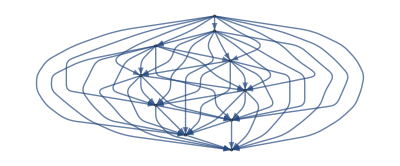

```mathematica
AdjacencyGraph[Table[PadRight[Table[1,{i-1}],10],{i,10}]]
```

```mathematica
MatrixForm/@Table[Table[PadRight[Table[1,{i-j}],3],{i,3}],{j,1,3-1}]
```

{(0 | 0 | 0
1 | 0 | 0
1 | 1 | 0),(0 | 0 | 0
0 | 0 | 0
1 | 0 | 0)}

```mathematica
2^25
```

33554432

```mathematica
DAGNumber[n_]:=2^(n^2-1)/2
```

```mathematica
DAGNumber[5]
```

8388608

```mathematica
Table[DAGNumber[i],{i,2,8}]
```

{4,128,16384,8388608,17179869184,140737488355328,4611686018427387904}

```mathematica
Table[2^i,{i,2,10}]
```

{4,8,16,32,64,128,256,512,1024}

```mathematica
DAGModelGenerator[n_]:=Table[Table[PadRight[Table[1,{i-j}],n],{i,n}],{j,1,n-1}]
```

```mathematica
ConstantArray[0,{6,6}]
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
ReplacePart[ConstantArray[0,{6,6}],2->1]
```

{{0,0,0,0,0,0},1,{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
Clear[CreateGraphs]
```

```mathematica
CreateGraphs[x_]:=Module[{graphs=DAGModelGenerator[6]},ReplacePart[ConstantArray[0,{6,6}],x->#]&@graphs[[x]]]
```

```mathematica
ConstantArray[0,{6,6}]
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
DAGModelGenerator[6]
```

{{{0,0,0,0,0,0},{1,0,0,0,0,0},{1,1,0,0,0,0},{1,1,1,0,0,0},{1,1,1,1,0,0},{1,1,1,1,1,0}},{{0,0,0,0,0,0},{0,0,0,0,0,0},{1,0,0,0,0,0},{1,1,0,0,0,0},{1,1,1,0,0,0},{1,1,1,1,0,0}},{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{1,0,0,0,0,0},{1,1,0,0,0,0},{1,1,1,0,0,0}},{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{1,0,0,0,0,0},{1,1,0,0,0,0}},{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{1,0,0,0,0,0}}}

```mathematica
(Map[PadRight[#,6]&,Table[Tuples[{0,1},{i}],{i,0,6}],{2}])[[3]]
```

{{0,0,0,0,0,0},{0,1,0,0,0,0},{1,0,0,0,0,0},{1,1,0,0,0,0}}

```mathematica
MatrixForm/@DAGModelGenerator[6]
```

{(0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0),(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0)}

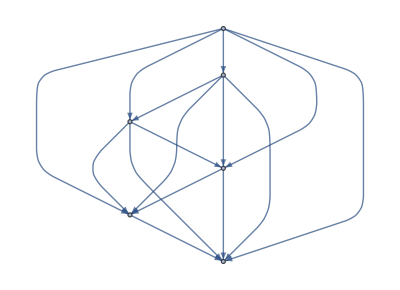
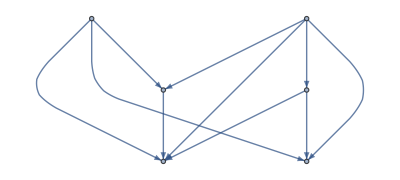
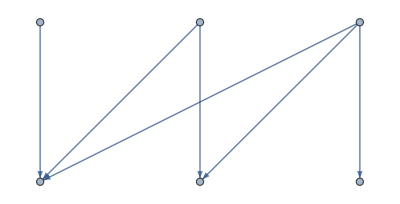
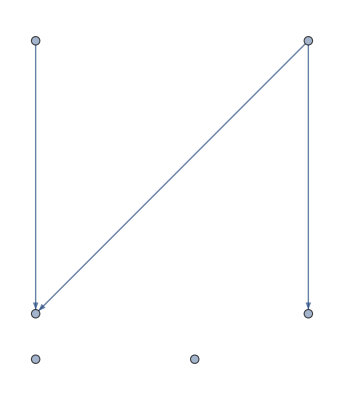
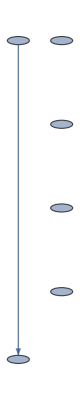

```mathematica
AdjacencyGraph/@DAGModelGenerator[6]
```

```mathematica
Tuples[Tuples[{0,1},3],3]
```

{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,1}},{{0,0,0},{0,0,0},{0,1,0}},{{0,0,0},{0,0,0},{0,1,1}},505,{{1,1,1},{1,1,1},{1,0,1}},{{1,1,1},{1,1,1},{1,1,0}},{{1,1,1},{1,1,1},{1,1,1}}}
 |  |  |  |

```mathematica
ConstantArray[0,{6,6}]
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
IntegerDigits[100,2]
```

{1,1,0,0,1,0,0}

```mathematica
2^64
```

18446744073709551616

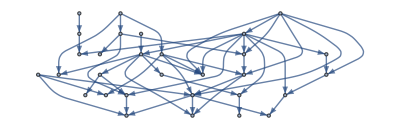

```mathematica
DirectedGraph[RandomGraph[BernoulliGraphDistribution[30,0.1]],"Acyclic"]
```

```mathematica
WeaklyConnectedGraphQ[%]
```

True

```mathematica
Module[{graph=TransitiveReductionGraph[DirectedGraph[RandomGraph[BernoulliGraphDistribution[400,0.005]],"Acyclic"]]},Max[Flatten[Table[FindPath[graph,i,j],{i,VertexCount[graph]},{j,VertexCount[graph]}]]]]
```

400

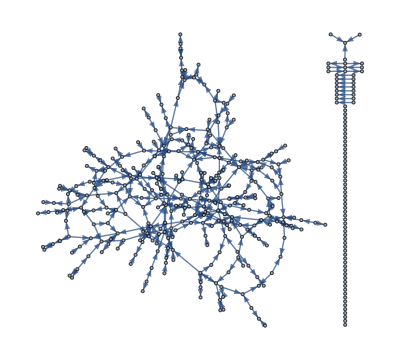

```mathematica
DAGraph=TransitiveReductionGraph[DirectedGraph[RandomGraph[BernoulliGraphDistribution[400,0.005]],"Acyclic"]]
```

```mathematica
ExtractGraphMajorComponent[graph_]:=Graph[Flatten[Cases[EdgeList[graph],x_/;x[[1]]==#]&/@WeaklyConnectedComponents[graph][[1]]],VertexLabels->"Name"]
```

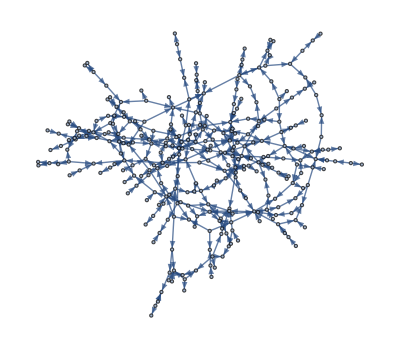

```mathematica
ExtractGraphMajorComponent[DAGraph]
```

```mathematica
CreateDAG[nodesize_,edgedensity_]:=ExtractGraphMajorComponent[TransitiveReductionGraph[DirectedGraph[RandomGraph[BernoulliGraphDistribution[nodesize,edgedensity]],"Acyclic"]]]
```

```mathematica
dag=CreateDAG[400,0.003];
```

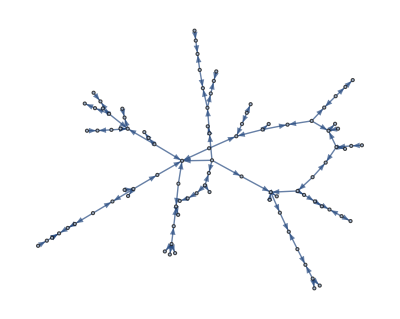

```mathematica
dag
```

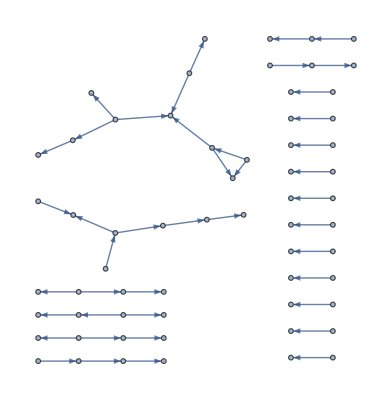

```mathematica
Graph[If[RandomInteger[1]<1,#[[1]]->#[[2]],#[[2]]->#[[1]]]&/@EdgeList@RandomGraph[BernoulliGraphDistribution[100,0.01]]]
```

```mathematica
Table[AcyclicGraphQ[Graph[If[RandomInteger[1]<1,#[[1]]->#[[2]],#[[2]]->#[[1]]]&/@EdgeList@RandomGraph[BernoulliGraphDistribution[100,i]]]],{i,0.01,0.05,0.005}]
```

{True,True,False,False,False,False,False,False,False}

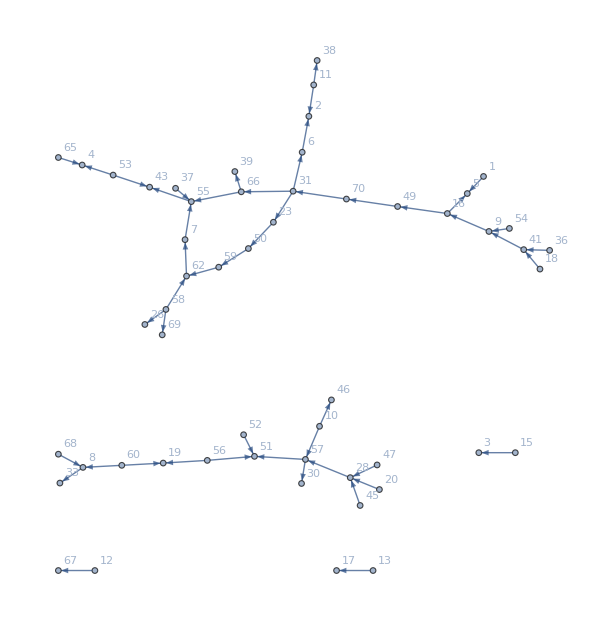

```mathematica
Graph[If[RandomInteger[1]<1,#[[1]]->#[[2]],#[[2]]->#[[1]]]&/@EdgeList@RandomGraph[BernoulliGraphDistribution[70,0.02]],VertexLabels->"Name"]
```

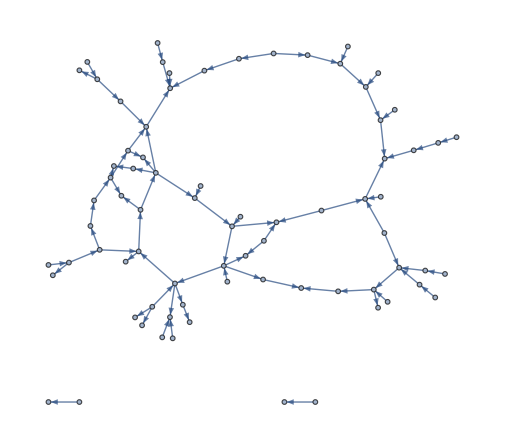
```mathematica
AcyclicGraphQ[-Graphics-]
```

False

```mathematica
contract[graph_]/;MemberQ[VertexDegree[graph],2]:=Module[{vd=VertexDegree[graph],vl=VertexList[graph],loc},loc=Cases[EdgeList[graph],UndirectedEdge[a___,b:vl[[First@FirstPosition[vd,2]]],c___]:>{a,b,c}][[1]];
VertexContract[graph,loc]]
```

```mathematica
Cases[EdgeList[graph],UndirectedEdge[a___,b:vl[[First@FirstPosition[vd,2]]],c___]:>{a,b,c}][[1]]
```

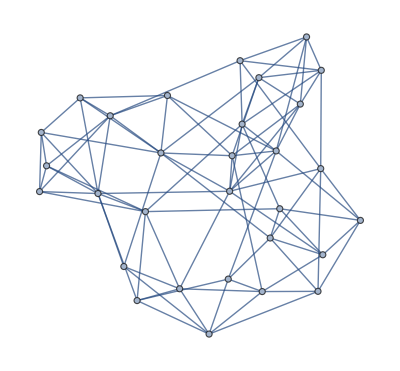

```mathematica
g=RandomGraph[WattsStrogatzGraphDistribution[30,0.3,3]]
```

```mathematica
methods={"Modularity","Centrality","CliquePercolation","Hierarchical","Spectral"}
```

{Modularity,Centrality,CliquePercolation,Hierarchical,Spectral}

```mathematica
CommunityGraphPlot[g,FindGraphCommunities[g,Method->#]]&/@methods
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MultiEdges[graph_]:=Rule@@@(First/@Select[Tally[Sort/@List@@@EdgeList[graph]],#[[2]]>1&])
```

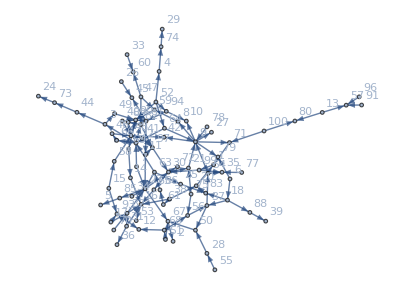

```mathematica
g=Graph[If[RandomInteger[1]<1,#[[1]]->#[[2]],#[[2]]->#[[1]]]&/@EdgeList[Graph[Flatten[Module[{graph=RandomGraph[BernoulliGraphDistribution[100,0.02]]},Cases[EdgeList[graph],x_/;x[[1]]==#]&/@ConnectedComponents[graph][[1]]]]]],VertexLabels->"Name"]
```

```mathematica
AcyclicGraphQ[g]
```

False

```mathematica
Clear[com]
```

```mathematica
com=FindGraphCommunities[g];
```

```mathematica
edgecoms=Table[Flatten[Cases[EdgeList[g],x_/;x[[1]]==#]&/@(com[[i]])],{i,Length[com]}];
```

```mathematica
edgecoms
```

{{30->65,30->72,30->21,65->16,31->16,31->36,16->53,32->16,32->23,32->31,23->30,23->67,23->85,34->23,85->5,14->16,69->14,70->32,17->32,17->93},{97->30,8->59,59->90,48->42,48->89,48->90,48->41,90->69,82->89,82->97,11->23,11->97,81->11,81->90,81->45,41->97,47->59,47->60,47->82,40->48,40->90,33->60,26->45},{9->10,9->27,9->42,9->71,9->79,9->8,64->9,64->22,78->9,94->10,94->81,52->64,52->90,52->94,52->4,4->74,74->29},{99->30,99->35,54->9,54->35,77->35,37->50,37->54,67->2,50->67,28->50,55->28},{20->1,1->99,71->1,38->20,38->61,38->16,83->20,61->86,86->63,63->25,63->23,63->22,25->83},{21->9,75->21,75->56,56->37,58->48,93->12,68->56,68->12,51->67,51->68,15->58,15->93},{22->66,22->82,22->3,66->46,7->22,7->23,46->48,3->44,3->49,44->73,49->90,73->24},{100->71,100->80,13->57,13->80,91->57,96->57},{18->37,18->83,18->88,88->39,6->18,6->79}}

```mathematica
Table[edgecom[i]=Select[edgecoms,Length[#]<i&],{i,5,20}];
```

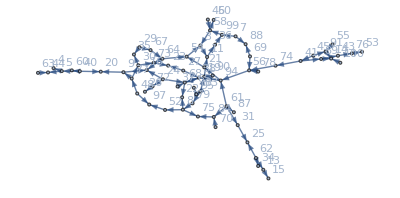

```mathematica
g
```

```mathematica
(EdgeDelete[#,MultiEdges[#]]&/@Table[Fold[EdgeContract[#1,#2]&,g,List@@@edgecom[i]],{i,5,20}])
```

```mathematica
AcyclicGraphQ/@(EdgeDelete[#,MultiEdges[#]]&/@Table[Fold[EdgeContract[#1,#2]&,g,List@@@edgecom[i]],{i,5,20}])
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

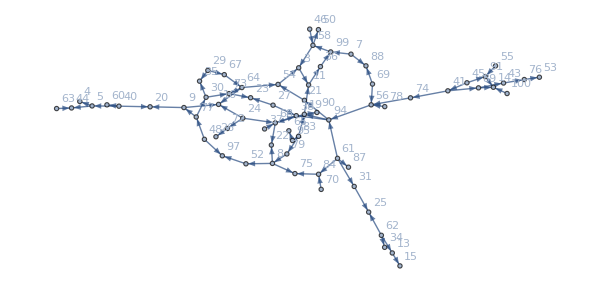
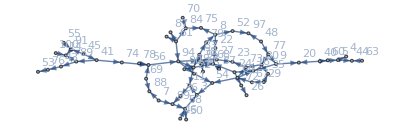
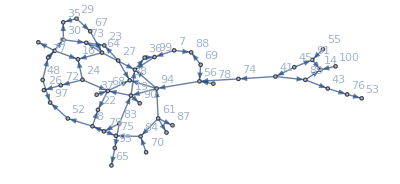
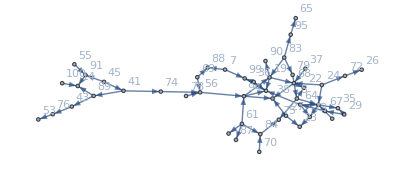
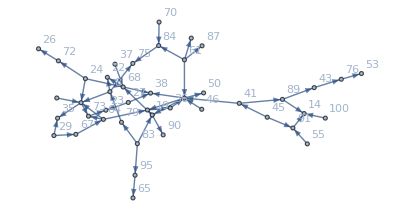
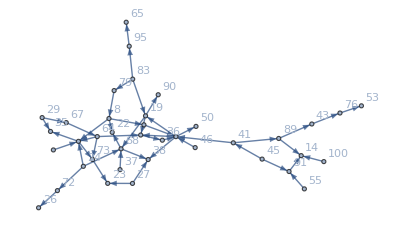
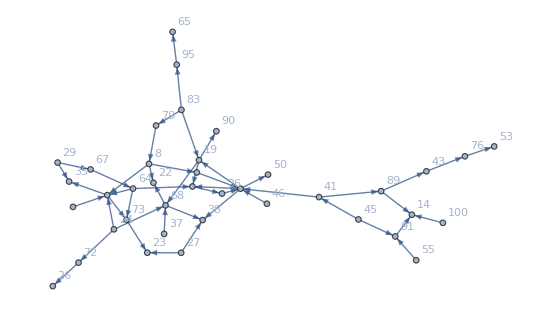
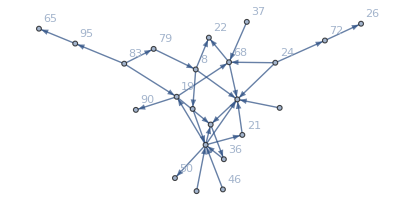
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(EdgeDelete[#,MultiEdges[#]]&/@Table[Fold[EdgeContract[#1,#2]&,g,List@@@edgecom[i]],{i,5,20}])
```

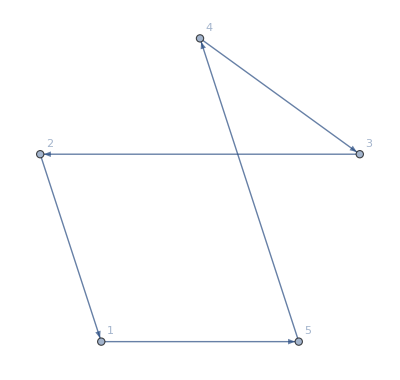

```mathematica
sq=Graph[Rule@@@(If[RandomInteger[1]<1,#[[1]]->#[[2]],#[[2]]->#[[1]]]&/@EdgeList[-Graphics-]),VertexLabels->"Name"]
```

```mathematica
EdgeList[-Graphics-]
```

{1<->2,1<->5,2<->3,3<->4,4<->5}

```mathematica
EdgeList[EdgeContract[sq,2->1]]
```

{4->3,5->4,1->5,3->1}

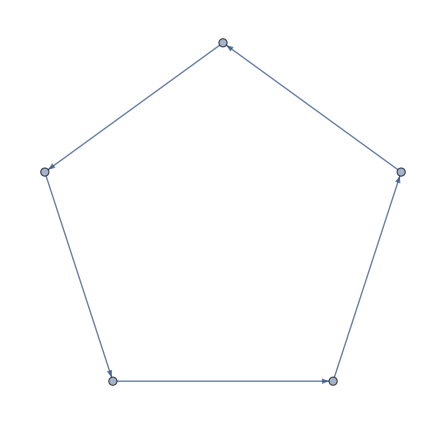

```mathematica
Graph[Rule@@@{1<->2,2<->3,3<->4,4<->5,5<->1}]
```

```mathematica
EdgeList[Graph[Rule@@@{1<->2,2<->3,3<->4,4<->5,5<->1}]]
```

{1->2,2->3,3->4,4->5,5->1}

```mathematica
AcyclicGraphQ[Graph[Rule@@@{1<->2,2<->3,3<->4,4<->5,5<->1}]]
```

False

```mathematica
AcyclicGraphQ[Graph[{1->2,2->3,3<->4,4->5,5->1}]]
```

False

```mathematica
ConnectedGraphQ[Graph[Rule@@@{1<->2,2<->3,3<->4,4<->5,5<->1}]]
```

True

```mathematica
AcyclicGraphQ[Graph[{1->2,2->3,3->4,4->5,5->1},VertexLabels->"Name"]]
```

False

```mathematica
AcyclicGraphQ[Graph[{1->2,2->3,3->"a",4->"a",4->5,5->1},VertexLabels->"Name"]]
```

True

```mathematica
DeleteCycle[graph_,cycles_]:=Module[{randomnode=RandomInteger[1000]+VertexCount[graph]},EdgeAdd[EdgeDelete[g,Union[Flatten@(First/@cycles)]],Union[Flatten@Table[{cycles[[i]][[1]][[1]]->randomnode,cycles[[i]][[1]][[2]]->randomnode},{i,Length[cycles]}]]]]
```

```mathematica
g=Graph[If[RandomInteger[1]<1,#[[1]]->#[[2]],#[[2]]->#[[1]]]&/@EdgeList[Graph[Flatten[Module[{graph=RandomGraph[BernoulliGraphDistribution[500,0.005]]},Cases[EdgeList[graph],x_/;x[[1]]==#]&/@ConnectedComponents[graph][[1]]]]]]];
```

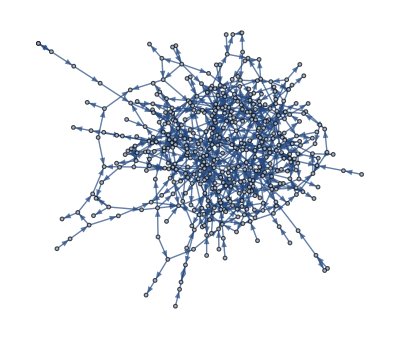

```mathematica
Graph[EdgeList[g]]
```

Low edge density leads to DAG with high probability, there seems to be a threshold, that appears to be different to the Erdos-Rényi threshold but not discarded a function of the Erdos-Rényi threshold. High edge density leads to an increase of large cycles. Large cycles, however, are part of the smaller ones with high probability so the collapse of the small ones destroys the large ones. We have thus two regimes of small non-causal patches and the rest of the graph cycle-free. Non-causal patches would have properties reminiscent of elementary particles, where apparent randomness would be the consequence of local non-causal relations.

```mathematica
AcyclicGraphQ[g]
```

False

```mathematica
Length/@Table[FindCycle[g,{i},100],{i,3,50}]
```

{1,0,0,1,0,0,1,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

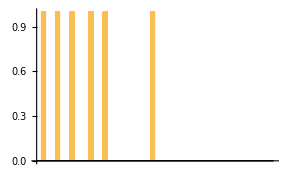
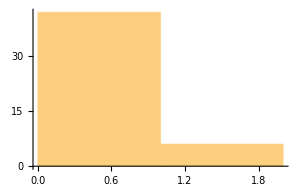

```mathematica
Row[{BarChart[Length/@Table[FindCycle[g,{i},100],{i,3,50}],ImageSize->290],Histogram[Length/@Table[FindCycle[g,{i},100],{i,3,50}],ImageSize->300]}]
```

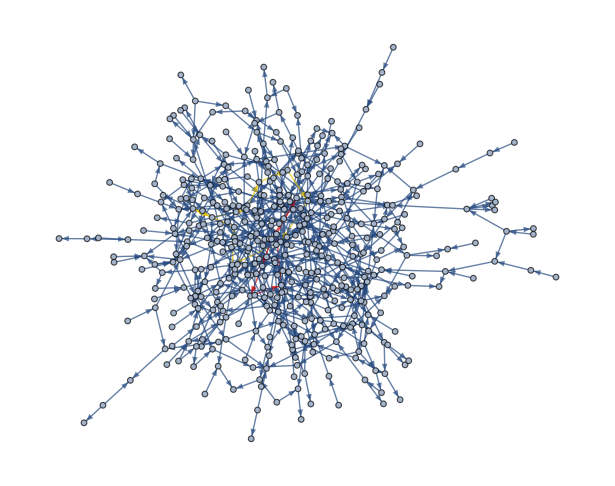

```mathematica
HighlightGraph[g,FindCycle[g,{4,10},100]]
```

```mathematica
AcyclicGraphQ[TransitiveReductionGraph[g]]
```

False

```mathematica
FindCycle[DeleteCycle[g,FindCycle[g,{3,6},100]],{3,6},100]
```

{}

```mathematica
AcyclicGraphQ[DeleteCycle[g,FindCycle[g,{3,500},100]]]
```

False

```mathematica
Length/@Table[FindCycle[g,{i},100],{i,3,50}]
```

{1,1,0,0,0,0,1,3,0,1,2,2,1,3,2,3,4,3,0,6,1,4,7,2,2,9,2,1,6,5,0,7,4,3,7,7,0,2,3,1,2,1,0,0,1,0,0,0}

```mathematica
Length/@Table[FindCycle[DeleteCycle[g,FindCycle[g,{4,7},100]],{i},100],{i,3,50}]
```

{1,0,0,0,0,0,1,3,0,1,2,2,1,3,2,3,4,3,0,6,1,4,7,2,2,9,2,1,6,5,0,7,4,3,7,7,0,2,3,1,2,1,0,0,1,0,0,0}

Causal networks with long cycles are unviable but universes with local cycles impose the an interesting two regime network where at the small scale random can appear from a deterministic model but at the large scale the network is causal and stable. Deletion of small cycles destroys all other larger cycles:

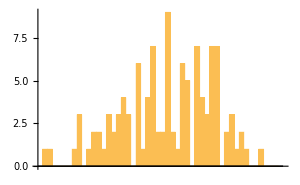
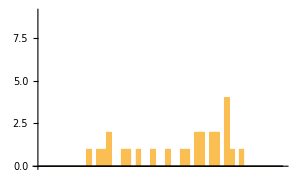

```mathematica
Row[{BarChart[Length/@Table[FindCycle[g,{i},100],{i,3,50}],ImageSize->300],BarChart[Length/@Table[FindCycle[DeleteCycle[g,FindCycle[g,{3,10},100]],{i},100],{i,3,50}],ImageSize->300,PlotRange->{0,9}]}]
```

```mathematica
Clear[g2]
```

```mathematica
Dynamic[i]
```

```mathematica
g2=Table[Graph[If[RandomInteger[1]<1,#[[1]]->#[[2]],#[[2]]->#[[1]]]&/@EdgeList[Graph[Flatten[Module[{graph=RandomGraph[BernoulliGraphDistribution[1000,i]]},Cases[EdgeList[graph],x_/;x[[1]]==#]&/@ConnectedComponents[graph][[1]]]]]]],{i,0.001,0.0025,0.0001}];
```

The greatest component of a large ER graph with very low edge density appears to be more Lorentzian (compare to Sprinkling method nets). In summary, it appears that the least fine-tuned model is a spare ER network model where not even causality is imposed but emergent, and on which small local non-causal patches behave quantum mechanical as particles. Other topologies with non-uniform nodes significantly increase the number of cycles, because they connect through the hubs, and appear non-Lorentzian.

```mathematica
VertexCount[#]&/@g2
```

{46,77,376,360,437,601,552,669,756,771,797,822,850,866,895,910}

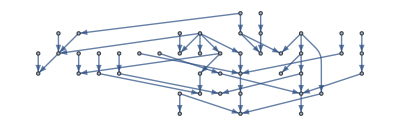
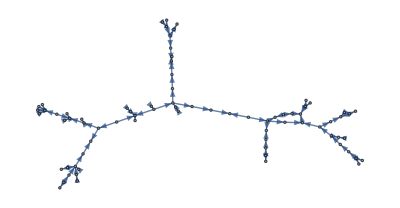
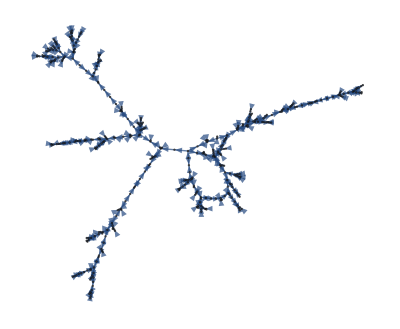
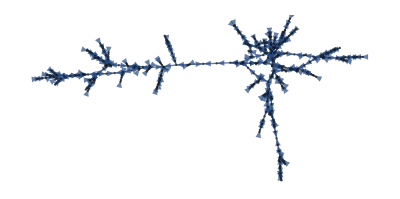
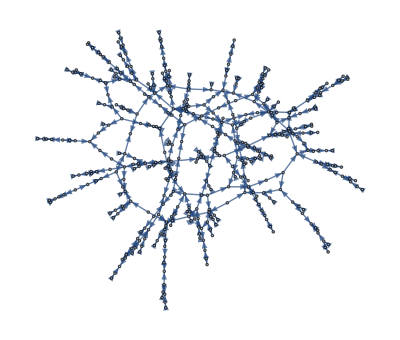
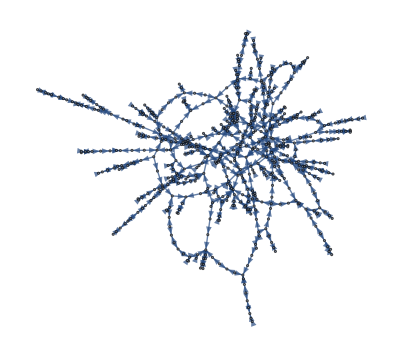

```mathematica
Graph[EdgeList[#]]&/@g2[[1;;6]]
```

They also appear naturally acyclic with probability near 1 for sparse networks, and asymptotically approaching density 0 as a function of edge density.

```mathematica
AcyclicGraphQ/@TransitiveReductionGraph/@g2
```

{True,True,True,True,True,False,True,True,True,True,False,False,False,False,False,False}

```mathematica
Length[g2]
```

16

```mathematica
Length/@(FindCycle[#,{3,20},100]&/@(TransitiveReductionGraph/@g2))
```

{0,0,0,0,0,1,0,0,0,0,4,1,1,3,0,0}

All cycles are short in sparse networks, but there is a quick transition to long and many cycles as a edge density increases, reaching a maximum for a fixed node size ER network:

```mathematica
Map[Length,Table[FindCycle[TransitiveReductionGraph@g2[[i]],{3,30},100],{i,1,Length[g2]}],{2}]
```

{{},{},{},{},{},{4},{},{},{},{},{3,4,5,11},{3},{7,30},{5,10,11,30},{},{}}

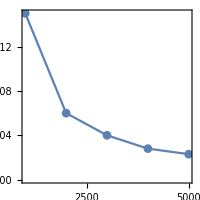

```mathematica
ListPlot[{{1000,0.0015},{2000,0.0006},{3000,0.0004},{4000,0.00028},{5000,0.00023}},PlotMarkers->Automatic,AspectRatio->1,ImageSize->200,Frame->True,Joined->True]
```

```mathematica
VertexCount/@(Graph[If[RandomInteger[1]<1,#[[1]]->#[[2]],#[[2]]->#[[1]]]&/@EdgeList[Graph[Flatten[Module[{graph=RandomGraph[BernoulliGraphDistribution[#[[1]],#[[2]]]]},Cases[EdgeList[graph],x_/;x[[1]]==#]&/@ConnectedComponents[graph][[1]]]]]]]&/@{{1000,0.0015},{2000,0.0006},{3000,0.0004},{4000,0.00028}})
```

{574,736,823,960}

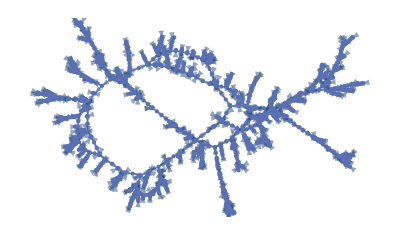

```mathematica
Graph[If[RandomInteger[1]<1,#[[1]]->#[[2]],#[[2]]->#[[1]]]&/@EdgeList[Graph[Flatten[Module[{graph=RandomGraph[BernoulliGraphDistribution[5000,0.00023]]},Cases[EdgeList[graph],x_/;x[[1]]==#]&/@ConnectedComponents[graph][[1]]]]]]]
```

```mathematica
VertexCount@%
```

1290

```mathematica
AcyclicGraphQ[-Graphics-]
```

True

Only when the network gets dense enough local cycles appear, in this case the sharp threshold is around 0.00033 for a network of size 5K when small local non-causal patches in the form of cycles appear, after which cycles start to grow in size:

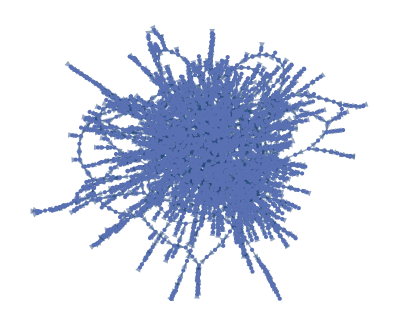

```mathematica
g3=Graph[If[RandomInteger[1]<1,#[[1]]->#[[2]],#[[2]]->#[[1]]]&/@EdgeList[Graph[Flatten[Module[{graph=RandomGraph[BernoulliGraphDistribution[5000,0.00032]]},Cases[EdgeList[graph],x_/;x[[1]]==#]&/@ConnectedComponents[graph][[1]]]]]]]
```

```mathematica
AcyclicGraphQ[g3]
```

True

```mathematica
AcyclicGraphQ[TransitiveReductionGraph[g3]]
```

True

```mathematica
Table[FindCycle[g3,{i},100],{i,3,20}]
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
Length/@Table[FindCycle[g3,{i},100],{i,3,20}]
```

{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

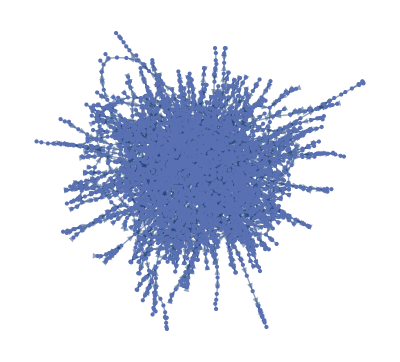

```mathematica
g4=Graph[If[RandomInteger[1]<1,#[[1]]->#[[2]],#[[2]]->#[[1]]]&/@EdgeList[Graph[Flatten[Module[{graph=RandomGraph[BernoulliGraphDistribution[5000,0.00035]]},Cases[EdgeList[graph],x_/;x[[1]]==#]&/@ConnectedComponents[graph][[1]]]]]]]
```

```mathematica
Limit
```

```mathematica
AcyclicGraphQ[g4]
```

False

```mathematica
Table[FindCycle[g4,{i},100],{i,3,20}]
```

{{},{},{},{},{{3409->3196,3196->879,879->3268,3268->1929,1929->3632,3632->102,102->3409}},{},{},{},{{4139->111,111->170,170->4302,4302->1536,1536->3726,3726->4530,4530->1485,1485->721,721->3334,3334->3844,3844->4139}},{},{},{},{},{},{},{},{},{}}

```mathematica
Length/@Table[FindCycle[g4,{i},100],{i,3,20}]
```

{0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0}

Thus larger cycles appear as a function of edge density making the network unviable.

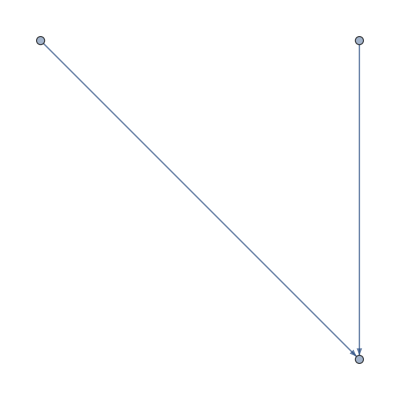

```mathematica
Graph[If[RandomInteger[1]<1,#[[1]]->#[[2]],#[[2]]->#[[1]]]&/@EdgeList[Graph[Flatten[Module[{graph=RandomGraph[BernoulliGraphDistribution[200,.01/10]]},Cases[EdgeList[graph],x_/;x[[1]]==#]&/@ConnectedComponents[graph][[1]]]]]]]
```

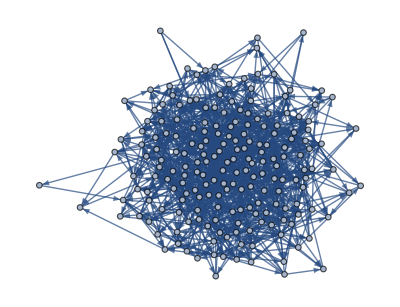

```mathematica
Graph[If[RandomInteger[1]<1,#[[1]]->#[[2]],#[[2]]->#[[1]]]&/@EdgeList[Graph[Flatten[Module[{graph=RandomGraph[BernoulliGraphDistribution[200,.5/10]]},Cases[EdgeList[graph],x_/;x[[1]]==#]&/@ConnectedComponents[graph][[1]]]]]]]
```

Taking a TransitiveReductionGraph imposes a threshold for cycle avoidance with < 0.05 avoiding cycles and only producing short ones if any, and > 0.05 producing cycles involving most of the network nodes. However, < 0.05  seems to generate structure and possibly Lorentzian nets.

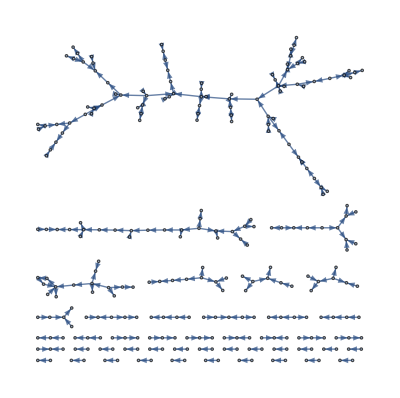

```mathematica
TransitiveReductionGraph@Graph[If[RandomInteger[1]<1,#[[1]]->#[[2]],#[[2]]->#[[1]]]&/@EdgeList[Graph[RandomGraph[BernoulliGraphDistribution[400,1/400]]]]]
```

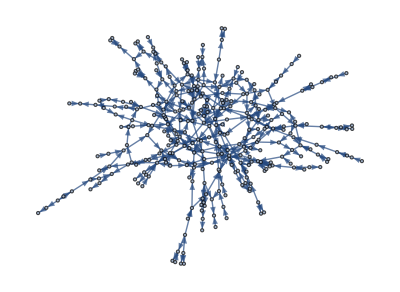

```mathematica
TransitiveReductionGraph@Graph[If[RandomInteger[1]<1,#[[1]]->#[[2]],#[[2]]->#[[1]]]&/@EdgeList[Graph[Flatten[Module[{graph=RandomGraph[BernoulliGraphDistribution[400,.05/10]]},Cases[EdgeList[graph],x_/;x[[1]]==#]&/@ConnectedComponents[graph][[1]]]]]]]
```

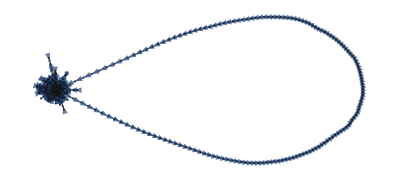

```mathematica
TransitiveReductionGraph@Graph[If[RandomInteger[1]<1,#[[1]]->#[[2]],#[[2]]->#[[1]]]&/@EdgeList[Graph[Flatten[Module[{graph=RandomGraph[BernoulliGraphDistribution[400,.07/10]]},Cases[EdgeList[graph],x_/;x[[1]]==#]&/@ConnectedComponents[graph][[1]]]]]]]
```

```mathematica
FindCycle[TransitiveReductionGraph@Graph[If[RandomInteger[1]<1,#[[1]]->#[[2]],#[[2]]->#[[1]]]&/@EdgeList[Graph[Flatten[Module[{graph=RandomGraph[BernoulliGraphDistribution[400,.05/10]]},Cases[EdgeList[graph],x_/;x[[1]]==#]&/@ConnectedComponents[graph][[1]]]]]]]]
```

{{358->21,21->368,368->73,73->128,128->358}}

```mathematica
points=MovingAverage[Flatten[(N/@Median/@Flatten/@Transpose[Table[Table[Length/@FindCycle[TransitiveReductionGraph@Graph[If[RandomInteger[1]<1,#[[1]]->#[[2]],#[[2]]->#[[1]]]&/@EdgeList[Graph[Flatten[Module[{graph=RandomGraph[BernoulliGraphDistribution[200,i/10]]},Cases[EdgeList[graph],x_/;x[[1]]==#]&/@ConnectedComponents[graph][[1]]]]]]]],{i,.01,2,.05}],10]]/200)/.{}->0],10]
```

```mathematica
points={0,0,0,0.07975,0.07675000000000001,0.07375000000000001,0.064,0.063,0.058499999999999996,0.05275000000000001,0.04175,0.03975000000000001,0.0345,0.03425,0.03150000000000001,0.0335,0.03275,0.0315,0.03725,0.036000000000000004,0.03475,0.038000000000000006,0.038000000000000006,0.035,0.036,0.03225,0.03175,0.0325,0.026750000000000003,0.026500000000000003,0.027000000000000003}
```

{0,0,0,0.07975,0.07675,0.07375,0.064,0.063,0.0585,0.05275,0.04175,0.03975,0.0345,0.03425,0.0315,0.0335,0.03275,0.0315,0.03725,0.036,0.03475,0.038,0.038,0.035,0.036,0.03225,0.03175,0.0325,0.02675,0.0265,0.027}

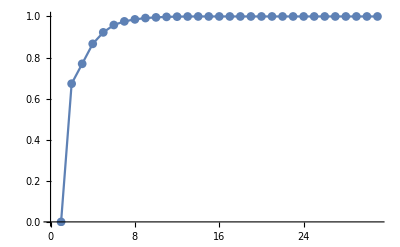

```mathematica
ListLinePlot[points2,PlotMarkers->Automatic]
```

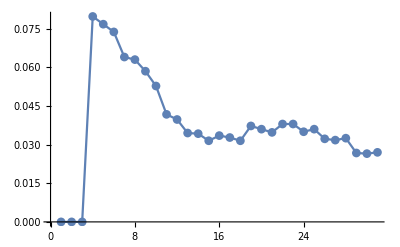

```mathematica
ListLinePlot[points,PlotMarkers->Automatic]
```

Relaxing the connectedness requirement:

```mathematica
20/10000=100 n
```

```mathematica
Solve[20/10000==100 n,n]
```

{{n→1/50000}}

```mathematica
Solve[10/10000==200 n,n]
```

{{n→1/200000}}

```mathematica
Solve[5/10000==400 n,n]
```

{{n→1/800000}}

```mathematica
Solve[3/10000==600 n,n]
```

{{n→1/2000000}}

```mathematica
80 4
```

320

```mathematica
100,200,400,600
```

```mathematica
320 4
```

1280

```mathematica
FindSequenceFunction[{5,20,80,320,1280},x]
```

5 4^(-1+x)

```mathematica
ThresholdFunction[nodes_]:=5 4^(-1+nodes/100)/1000.
```

```mathematica
ThresholdFunction[800]
```

81.92

```mathematica
(graphsize/100)/500/(graphsize/100)^2.
```

0.002

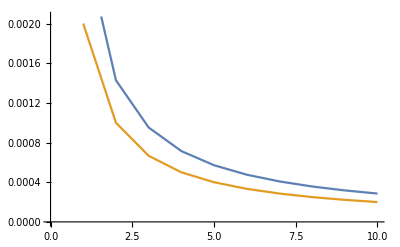

```mathematica
ListLinePlot[{Table[(1/x)/350,{x,1,10}],Table[(x/5)/(x^2.),{x,1,10}]/100}]
```

```mathematica
Table[x/500/x^2.,{x,100/100,800/100}]
```

{0.002,0.001,0.000666667,0.0005,0.0004,0.000333333,0.000285714,0.00025}

```mathematica
20/10000.
```

0.002

```mathematica
10/10000.
```

0.001

```mathematica
5/10000.
```

0.0005

```mathematica
3/10000.
```

0.0003

```mathematica
(5 2^(800/100/2))/10000.
```

0.008

```mathematica
Join[{3},Table[5 2^n,{n,0,3}]]
```

{3,5,10,20,40}

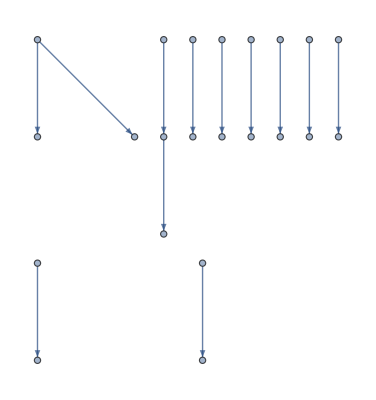

```mathematica
Module[{graphsize=100},TransitiveReductionGraph[Graph[If[RandomInteger[1]<1,#[[1]]->#[[2]],#[[2]]->#[[1]]]&/@EdgeList[RandomGraph[BernoulliGraphDistribution[graphsize, (graphsize/100)/500/(graphsize/100)^2]]]]]]
```

```mathematica
points3=MovingAverage[Flatten[(N/@Median/@(Flatten/@Transpose[Table[Table[Length/@FindCycle[TransitiveReductionGraph@Graph[If[RandomInteger[1]<1,#[[1]]->#[[2]],#[[2]]->#[[1]]]&/@EdgeList[RandomGraph[BernoulliGraphDistribution[400,i/10]]]]],{i,.01,2,.05}],10]]/400)/.{}->0)],10]
```

Median::rectt: Rectangular array expected at position 1 in Median[0].

{1/10 (7.6325+Median[0]),0.86325,0.956625,0.9855,0.99425,0.99825,0.9995,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
points3={0,1.7200000000000004,1.9145,1.9737500000000001,1.9917500000000001,1.9962499999999999,1.9987500000000002,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.}/2
```

{0,0.86,0.95725,0.986875,0.995875,0.998125,0.999375,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

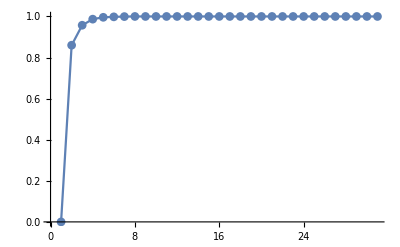

```mathematica
ListLinePlot[points3,PlotMarkers->Automatic]
```

```mathematica
FindCycle[TransitiveReductionGraph@RandomGraph[BernoulliGraphDistribution[400,.01]]]
```

{}

```mathematica
points4=MovingAverage[Flatten[(N/@Median/@(Flatten/@Transpose[Table[Table[Length/@FindCycle[TransitiveReductionGraph@Graph[If[RandomInteger[1]<1,#[[1]]->#[[2]],#[[2]]->#[[1]]]&/@EdgeList[RandomGraph[BernoulliGraphDistribution[400,i/10]]]]],{i,.01,2,.05}],10]]/400)/.{}->0)],10]
```

Median::rectt: Rectangular array expected at position 1 in Median[0].

{1/10 (7.6275+Median[0]),0.86275,0.95525,0.9855,0.9945,0.9985,0.999375,0.999875,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

When considering undirected ER graphs, the percolation (edge density) threshold 1/x, with x the number of nodes, after transitive reduction determines the existence of a giant component. However, for randomly directed ER graphs after transitive reduction, the percolation threshold determines the existence of a giant cycle above which most nodes in the network belong to the giant cycle and below which no cycles exist, thus sharp dividing the networks between causal and non-causal. Networks at the threshold, however, create few small cycles that violate causality in what could be similar to retro-causality, the relaxation of the causality requirement may model non-local quantum effects. Without transitive reduction, however, the probability of a node to be in a cycle in an ER graph is at most 0.20 at the percolation threshold but asymptotically vanishes reaching 0 in the limit as a function of edge density. This means that causality from randomly directed graphs can be an emergent property from ER graphs without any transitive reduction or connectivity requirement and for transitive reduced graphs, there is a sharp separation between causal and non-causal networks thereby making edge density fine-tuning the unlikely borderline case and, for the transitive reduction, a clear cut between the most likely either causal or non-causal regimes, with the 2 regimes of small non-causal cycles in a larger causal component, interacting with each other where highest algorithmic complexity is reached and from which it dramatically suddenly drops afterwards after becoming mostly a cycle graph in the transitive reduced case.

```mathematica
GetHD[g_]:=Module[{g2=AdjacencyGraph[AdjacencyMatrix[g]]},Module[{gdm,centraledge,n,vc,gcs},gdm=GraphDistanceMatrix[UndirectedGraph[g2]];
n=1;
vc=VertexCount[g2];gcs=GraphCenter[UndirectedGraph[g2]];
centraledge=gcs[[Ceiling[Length[gcs]/2]]];
While[Length[Select[gdm[[centraledge]],#≤n&]]<vc/2,n=n;
n++];Log[n,Length[Select[gdm[[centraledge]],#≤n&]]]]]
```

```mathematica
Dynamic[i]
```

```mathematica
dimensions=(Flatten/@Transpose[Table[Table[GetHD[ExtractGraphMajorComponent[TransitiveReductionGraph@Graph[If[RandomInteger[1]<1,#[[1]]->#[[2]],#[[2]]->#[[1]]]&/@EdgeList[RandomGraph[BernoulliGraphDistribution[500,i/10]]]]]],{i,.01,2,.05}],10]]/400);
```